{ | «1»

L→1.06233

H→1.

m→2.39556

-Graphics3D-

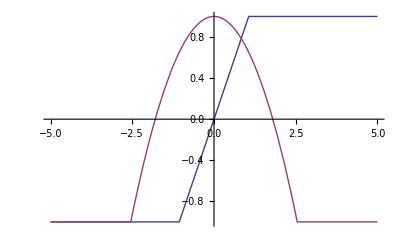

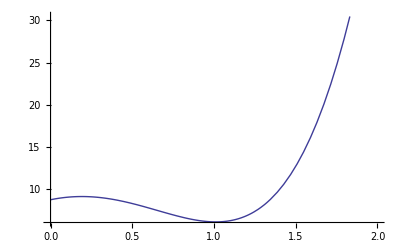

```mathematica
f11[x_,L_]:=Which[-L≤ x≤ L,x/(L),x>L,1,x<-L,-1];
f12[x_,L_,H_,m_]:=If[-m L≤x≤m L,-(1+H)((x/(m L))^2)+H,-1];
gamma=0.2;
delta1=0.2;
delta2=0.2;
res[L_,H_,m_]=Integrate[(D[f11[x,L],x]^2+D[f12[x,L,H,m],x]^2)/2+((f11[x,L]^2-1)^2(f11[x,L]^2-delta1)+((f12[x,L,H,m]^2-1)^2-(delta2/4)(f12[x,L,H,m]-2)(f12[x,L,H,m]+1)^2)/(f11[x,L]^2+gamma)),{x,-5,5}]
min=FindMinimum[{res[L,H,m],H≤1},{L,1},{H,1},{m,2}];
cor=min[[2]][[1]]
haut=min[[2]][[2]]
large=min[[2]][[3]]
Plot3D[res[L,H,m/.large],{L,0,2},{H,0,1}]
Plot[{f11[x,L/.cor],f12[x,L/.cor,H/.haut,m/.large]},{x,-5,5},PlotRange->All]
res2[H_]=res[L,H,m]/.cor/.large;
Plot[res2[H],{H,0,2}]
```